# ログ分析：ユーザーキーワード連鎖、推測、レコメンド

## 変数

```mathematica
datestr="20231001"
```

20231001

```mathematica
dir="/Users/kouamano/NII/togo-log/rcoslogs/log/M=202310-202312/"
```

/Users/kouamano/NII/togo-log/rcoslogs/log/M=202310-202312/

```mathematica
datafile=dir<>"D="<>datestr<>"/T=4/_story/log-analysis_"<>datestr<>"_vocLGraph.save"
```

/Users/kouamano/NII/togo-log/rcoslogs/log/M=202310-202312/D=20231001/T=4/_story/log-analysis_20231001_vocLGraph.save

## Data

```mathematica
Get[datafile];
```

```mathematica
storyVocLGrSel[4,"voc"]["20231001"]//Length
```

121359

## Program

キーワードをグラフvertexのラベルにする：
CiNiiの場合、オプションがKWに後続するので "&" 以降は切って良い。

```mathematica
URLtoKW[v_String]:=Module[{l},
l=StringSplit[v,"?q="];
If[Length[l]<2,Null,StringSplit[l[[2]],"&"][[1]]//URLDecode]
]
URLtoKW[v_List]:=Module[{l},
l=StringSplit[v[[1]],"?q="];
If[Length[l]<2,Null,StringSplit[l[[2]],"&"][[1]]//URLDecode]
]
```

```mathematica
VtoVLRl[v_List]:=Map[#->URLtoKW[#]&,v]
```

```mathematica
(*GtoKWSeq[g_Graph]:=({URLtoKW[#1⟦1⟧],#1⟦2⟧}&)/@SortBy[Cases[VertexList[g],{_,{_}}],#1⟦2,1⟧&]*)
```

```mathematica
GtoKWSeq[g_Graph]:=({URLtoKW[#1⟦1⟧],#1⟦2⟧}&)/@SortBy[Cases[VertexList[g],{_,{__}}],#1⟦2,1⟧&]
```

```mathematica
KWSeqSplitGather[kws_]:=Map[#[[1]]&,Split[DeleteCases[Map[#[[1]]&,kws],Null]]]
```

## 試験

### ノード数

```mathematica
nodecount["20231001"]=SortBy[Tally[Map[VertexCount,storyVocLGrSel[4,"voc"]["20231001"]]],First]
```

{{2,96834},{3,9483},{4,3863},{5,2225},{6,1600},{7,1148},{8,893},{9,708},{10,587},{11,472},{12,382},{13,361},{14,286},{15,270},{16,221},{17,187},{18,181},{19,150},{20,136},{21,117},{22,103},{23,92},{24,75},{25,77},{26,79},{27,65},{28,56},{29,44},{30,44},{31,49},{32,33},{33,31},{34,36},{35,22},{36,26},{37,20},{38,21},{39,27},{40,21},{41,10},{42,19},{43,17},{44,8},{45,16},{46,10},{47,9},{48,11},{49,8},{50,5},{51,10},{52,10},{53,9},{54,7},{55,6},{56,6},{57,9},{58,3},{59,3},{60,5},{61,14},{62,2},{63,6},{64,1},{65,5},{66,5},{67,8},{68,7},{69,5},{70,4},{72,4},{73,1},{74,4},{75,1},{76,1},{77,2},{78,3},{79,1},{80,2},{82,3},{83,2},{84,1},{85,2},{86,2},{87,2},{88,1},{89,1},{90,4},{91,1},{92,1},{93,1},{94,2},{95,2},{96,1},{98,2},{99,1},{101,1},{105,1},{106,1},{107,2},{108,1},{111,1},{113,1},{114,1},{115,1},{116,1},{117,1},{118,1},{119,1},{121,2},{130,1},{132,1},{134,1},{135,1},{139,1},{140,1},{151,1},{157,1},{160,1},{170,1},{189,1},{200,1},{202,1},{210,1},{223,1},{229,2},{230,1},{259,1},{262,1},{273,1},{283,2},{285,1},{288,1},{297,1},{299,1},{334,2},{396,1},{996,1},{1079,1}}

```mathematica
nodecountTotal["20231001"]=Map[#[[2]]&,nodecount["20231001"]]//Total
```

121359

```mathematica
Position[Map[VertexCount,storyVocLGrSel[4,"voc"]["20231001"]],14][[1;;10]]
```

{{420},{704},{1297},{1304},{1364},{1404},{1413},{1527},{1700},{1962}}

### アクセスグラフ選択の検討

同一テーマにおけるキーワードの変遷が欲しい。
そのためグラフのチェインが比較的短い（ノード数が少ない）もののみを選択する。
時間で切る方法もあるが、今の所採用しない想定。

経験的に同一テーマでの検索であってもは100近くの訪問を生じることがある。
さらに確実にするため最大50程度とする。

カバーの確認：
40nodesでも99%以上をカバーしている。40にするか？

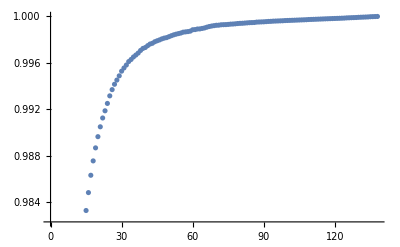

```mathematica
ListPlot[Accumulate[Map[#[[2]]&,nodecount["20231001"]]]/nodecountTotal["20231001"]]
```

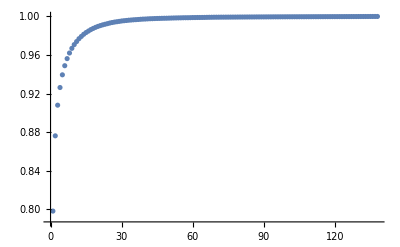

```mathematica
ListPlot[Accumulate[Map[#[[2]]&,nodecount["20231001"]]]/nodecountTotal["20231001"],PlotRange->Full]
```

### キーワード列生成の検討

ページを繰るごとにログが発生し同じキーワードが続く <- 連続同一キーワードの入力は一回とみなす。
キーワードなし（詳細ページ閲覧など）は無視する。

704 :

```mathematica
id=704
```

704

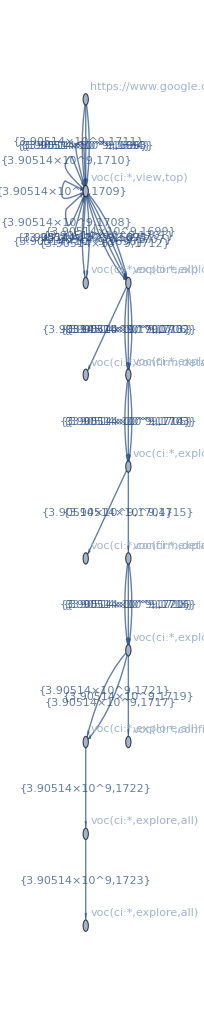

```mathematica
Graph[storyVocLGrSel[4,"voc"]["20231001"][[id]],VertexLabels->None]
```

VertexLabelとしてのvocを取り出す：

```mathematica
vocRl=PropertyValue[storyVocLGrSel[4,"voc"]["20231001"][[id]],VertexLabels]
```

{Name,{https://cir.nii.ac.jp/all?q=hauptomann,{3.90514×10^9,3.90514×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/,{3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9}}→voc[ci:*,view,top],{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=6,{3.90514×10^9,3.90514×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/crid/1522262180605190784,{3.90514×10^9}}→voc[ci:*,confirm,detail],{https://cir.nii.ac.jp/crid/1520291855057656576,{3.90514×10^9}}→voc[ci:*,confirm,detail],{https://cir.nii.ac.jp/crid/1020000781826138244,{3.90514×10^9}}→voc[ci:*,confirm,detail],{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=3,{3.90514×10^9,3.90514×10^9,3.90514×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=2,{3.90514×10^9,3.90514×10^9,3.90514×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=5,{3.90514×10^9,3.90514×10^9,3.90514×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=7,{3.90514×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=8,{3.90514×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8,{3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=4,{3.90514×10^9}}→voc[ci:*,explore,all],https://www.google.com/→https://www.google.com/}

ラベルルール：

```mathematica
vl=VertexList[storyVocLGrSel[4,"voc"]["20231001"][[id]]]//VtoVLRl
```

{{https://cir.nii.ac.jp/,{3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9}}→Null,https://www.google.com/→Null,{https://cir.nii.ac.jp/all?q=hauptomann,{3.90514×10^9,3.90514×10^9}}→hauptomann,{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8,{3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9}}→内野正幸,{https://cir.nii.ac.jp/crid/1020000781826138244,{3.90514×10^9}}→Null,{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=2,{3.90514×10^9,3.90514×10^9,3.90514×10^9}}→内野正幸,{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=3,{3.90514×10^9,3.90514×10^9,3.90514×10^9}}→内野正幸,{https://cir.nii.ac.jp/crid/1522262180605190784,{3.90514×10^9}}→Null,{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=4,{3.90514×10^9}}→内野正幸,{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=5,{3.90514×10^9,3.90514×10^9,3.90514×10^9}}→内野正幸,{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=6,{3.90514×10^9,3.90514×10^9}}→内野正幸,{https://cir.nii.ac.jp/crid/1520291855057656576,{3.90514×10^9}}→Null,{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=7,{3.90514×10^9}}→内野正幸,{https://cir.nii.ac.jp/all?q=%E5%86%85%E9%87%8E%E6%AD%A3%E5%B9%B8&page=8,{3.90514×10^9}}→内野正幸}

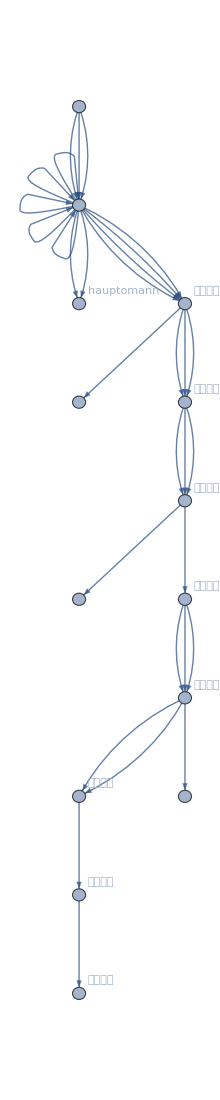

```mathematica
Graph[storyVocLGrSel[4,"voc"]["20231001"][[id]],VertexLabels->vl,EdgeLabels->None]
```

キーワードの時間的変遷：

```mathematica
GtoKWSeq[storyVocLGrSel[4,"voc"]["20231001"][[id]]]
```

{{hauptomann,{3.90514×10^9,3.90514×10^9}},{Null,{3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9}},{内野正幸,{3.90514×10^9,3.90514×10^9,3.90514×10^9,3.90514×10^9}},{Null,{3.90514×10^9}},{内野正幸,{3.90514×10^9,3.90514×10^9,3.90514×10^9}},{内野正幸,{3.90514×10^9,3.90514×10^9,3.90514×10^9}},{Null,{3.90514×10^9}},{内野正幸,{3.90514×10^9}},{内野正幸,{3.90514×10^9,3.90514×10^9,3.90514×10^9}},{内野正幸,{3.90514×10^9,3.90514×10^9}},{Null,{3.90514×10^9}},{内野正幸,{3.90514×10^9}},{内野正幸,{3.90514×10^9}}}

1297 :

```mathematica
id=1297
```

1297

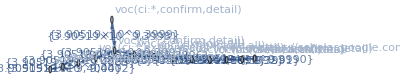

```mathematica
Graph[storyVocLGrSel[4,"voc"]["20231001"][[id]],VertexLabels->None]
```

VertexLabelとしてのvocを取り出す：

```mathematica
vocRl=PropertyValue[storyVocLGrSel[4,"voc"]["20231001"][[id]],VertexLabels]
```

{Name,{https://cir.nii.ac.jp/all?q=bending+metals&count=20&sortorder=0,{3.90519×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/all?q=MATERIALS%20TRANSACTIONS,{3.90519×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/crid/1110845735210214784,{3.90519×10^9}}→voc[ci:*,confirm,detail],{https://cir.nii.ac.jp/all?q=bending+of+metal&count=20&sortorder=0,{3.90519×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/data,{3.90519×10^9}}→voc[ci:*,search,data],{https://cir.nii.ac.jp/crid/1390859160311309568,{3.90519×10^9}}→voc[ci:*,confirm,detail],{https://cir.nii.ac.jp/all?q=sheet+metal+bending&count=20&sortorder=0,{3.90519×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/articles?q=metal+bending,{3.90519×10^9}}→voc[ci:*,search,articles],{https://cir.nii.ac.jp/crid/1410291767736863363,{3.90519×10^9}}→voc[ci:*,confirm,detail],{https://cir.nii.ac.jp/crid/1390291767736863360,{3.90519×10^9,3.90519×10^9}}→voc[ci:*,confirm,detail],https://scholar.google.com/→https://scholar.google.com/,{https://cir.nii.ac.jp/dissertations?q=bending%20of%20metal&sortorder=0,{3.90519×10^9,3.90519×10^9}}→voc[ci:*,search,dssertations],{https://cir.nii.ac.jp/all?q=Journal%20of%20the%20Japan%20Institute%20of%20Metals%20and%20Materials,{3.90519×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/crid/1130000794770852224,{3.90519×10^9}}→voc[ci:*,confirm,detail]}

ラベルルール：

```mathematica
vl=VertexList[storyVocLGrSel[4,"voc"]["20231001"][[id]]]//VtoVLRl
```

{https://scholar.google.com/→Null,{https://cir.nii.ac.jp/crid/1130000794770852224,{3.90519×10^9}}→Null,{https://cir.nii.ac.jp/data,{3.90519×10^9}}→Null,{https://cir.nii.ac.jp/articles?q=metal+bending,{3.90519×10^9}}→metal bending,{https://cir.nii.ac.jp/crid/1390859160311309568,{3.90519×10^9}}→Null,{https://cir.nii.ac.jp/all?q=Journal%20of%20the%20Japan%20Institute%20of%20Metals%20and%20Materials,{3.90519×10^9}}→Journal of the Japan Institute of Metals and Materials,{https://cir.nii.ac.jp/all?q=bending+metals&count=20&sortorder=0,{3.90519×10^9}}→bending metals,{https://cir.nii.ac.jp/all?q=sheet+metal+bending&count=20&sortorder=0,{3.90519×10^9}}→sheet metal bending,{https://cir.nii.ac.jp/crid/1390291767736863360,{3.90519×10^9,3.90519×10^9}}→Null,{https://cir.nii.ac.jp/crid/1410291767736863363,{3.90519×10^9}}→Null,{https://cir.nii.ac.jp/all?q=MATERIALS%20TRANSACTIONS,{3.90519×10^9}}→MATERIALS TRANSACTIONS,{https://cir.nii.ac.jp/all?q=bending+of+metal&count=20&sortorder=0,{3.90519×10^9}}→bending of metal,{https://cir.nii.ac.jp/dissertations?q=bending%20of%20metal&sortorder=0,{3.90519×10^9,3.90519×10^9}}→bending of metal,{https://cir.nii.ac.jp/crid/1110845735210214784,{3.90519×10^9}}→Null}

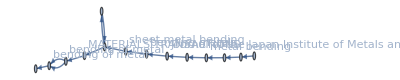

```mathematica
Graph[storyVocLGrSel[4,"voc"]["20231001"][[id]],VertexLabels->vl,EdgeLabels->None]
```

キーワードの時間的変遷：

```mathematica
kws[id]=GtoKWSeq[storyVocLGrSel[4,"voc"]["20231001"][[id]]]
```

{{Null,{3.90519×10^9}},{Null,{3.90519×10^9}},{metal bending,{3.90519×10^9}},{Null,{3.90519×10^9}},{Journal of the Japan Institute of Metals and Materials,{3.90519×10^9}},{bending metals,{3.90519×10^9}},{sheet metal bending,{3.90519×10^9}},{Null,{3.90519×10^9,3.90519×10^9}},{Null,{3.90519×10^9}},{MATERIALS TRANSACTIONS,{3.90519×10^9}},{bending of metal,{3.90519×10^9}},{bending of metal,{3.90519×10^9,3.90519×10^9}},{Null,{3.90519×10^9}}}

```mathematica
KWSeqSplitGather[kws[id]]//TableForm
```

metal bending
Journal of the Japan Institute of Metals and Materials
bending metals
sheet metal bending
MATERIALS TRANSACTIONS
bending of metal

1304 :

```mathematica
id=1304
```

1304

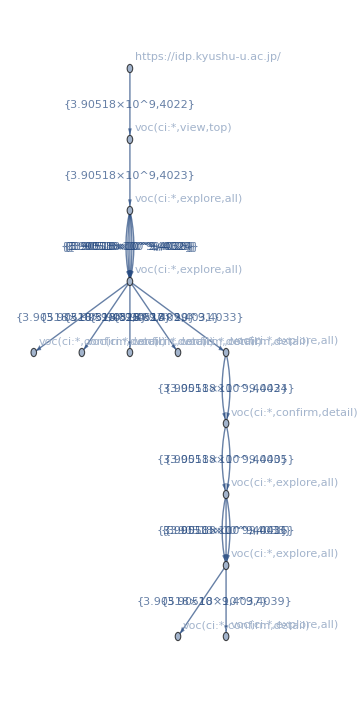

```mathematica
Graph[storyVocLGrSel[4,"voc"]["20231001"][[id]],VertexLabels->None]
```

VertexLabelとしてのvocを取り出す：

```mathematica
vocRl=PropertyValue[storyVocLGrSel[4,"voc"]["20231001"][[id]],VertexLabels]
```

{Name,{https://cir.nii.ac.jp/,{3.90518×10^9}}→voc[ci:*,view,top],{https://cir.nii.ac.jp/all?q=%E4%B8%AD%E5%9B%BD%E8%87%AA%E5%8B%95%E8%BB%8A&hasLinkToFullText=true&sortorder=0&page=2,{3.90518×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/crid/1050001338899573376,{3.90518×10^9,3.90518×10^9}}→voc[ci:*,confirm,detail],{https://cir.nii.ac.jp/crid/1050858298305404032,{3.90518×10^9}}→voc[ci:*,confirm,detail],{https://cir.nii.ac.jp/all?q=%E8%87%AA%E5%8B%95%E8%BB%8A%E8%BC%B8%E5%87%BA&hasLinkToFullText=true&sortorder=0&page=2,{3.90518×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/all?q=%E4%B8%AD%E5%9B%BD%E8%87%AA%E5%8B%95%E8%BB%8A&hasLinkToFullText=true,{3.90518×10^9,3.90518×10^9,3.90518×10^9,3.90518×10^9,3.90518×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/crid/1390574334792671744,{3.90518×10^9}}→voc[ci:*,confirm,detail],{https://cir.nii.ac.jp/crid/1390565134833695232,{3.90518×10^9}}→voc[ci:*,confirm,detail],{https://cir.nii.ac.jp/all?q=%E8%87%AA%E5%8B%95%E8%BB%8A%E8%BC%B8%E5%87%BA&hasLinkToFullText=true&hasLinkToFullText=true&count=20&sortorder=0,{3.90518×10^9,3.90518×10^9,3.90518×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/all?q=%E4%B8%AD%E5%9B%BD%E8%87%AA%E5%8B%95%E8%BB%8A,{3.90518×10^9}}→voc[ci:*,explore,all],{https://cir.nii.ac.jp/all?q=%E4%B8%AD%E5%9B%BD%E8%87%AA%E5%8B%95%E8%BB%8A&hasLinkToFullText=true&hasLinkToFullText=true,{3.90518×10^9,3.90518×10^9}}→voc[ci:*,explore,all],https://idp.kyushu-u.ac.jp/→https://idp.kyushu-u.ac.jp/,{https://cir.nii.ac.jp/crid/1390853649717300224,{3.90518×10^9}}→voc[ci:*,confirm,detail],{https://cir.nii.ac.jp/crid/1050845763925213312,{3.90518×10^9}}→voc[ci:*,confirm,detail]}

ラベルルール：

```mathematica
vl=VertexList[storyVocLGrSel[4,"voc"]["20231001"][[id]]]//VtoVLRl
```

{https://idp.kyushu-u.ac.jp/→Null,{https://cir.nii.ac.jp/,{3.90518×10^9}}→Null,{https://cir.nii.ac.jp/all?q=%E4%B8%AD%E5%9B%BD%E8%87%AA%E5%8B%95%E8%BB%8A,{3.90518×10^9}}→中国自動車,{https://cir.nii.ac.jp/all?q=%E4%B8%AD%E5%9B%BD%E8%87%AA%E5%8B%95%E8%BB%8A&hasLinkToFullText=true,{3.90518×10^9,3.90518×10^9,3.90518×10^9,3.90518×10^9,3.90518×10^9}}→中国自動車,{https://cir.nii.ac.jp/crid/1050858298305404032,{3.90518×10^9}}→Null,{https://cir.nii.ac.jp/crid/1390574334792671744,{3.90518×10^9}}→Null,{https://cir.nii.ac.jp/crid/1390853649717300224,{3.90518×10^9}}→Null,{https://cir.nii.ac.jp/crid/1390565134833695232,{3.90518×10^9}}→Null,{https://cir.nii.ac.jp/all?q=%E4%B8%AD%E5%9B%BD%E8%87%AA%E5%8B%95%E8%BB%8A&hasLinkToFullText=true&sortorder=0&page=2,{3.90518×10^9}}→中国自動車,{https://cir.nii.ac.jp/crid/1050001338899573376,{3.90518×10^9,3.90518×10^9}}→Null,{https://cir.nii.ac.jp/all?q=%E4%B8%AD%E5%9B%BD%E8%87%AA%E5%8B%95%E8%BB%8A&hasLinkToFullText=true&hasLinkToFullText=true,{3.90518×10^9,3.90518×10^9}}→中国自動車,{https://cir.nii.ac.jp/all?q=%E8%87%AA%E5%8B%95%E8%BB%8A%E8%BC%B8%E5%87%BA&hasLinkToFullText=true&hasLinkToFullText=true&count=20&sortorder=0,{3.90518×10^9,3.90518×10^9,3.90518×10^9}}→自動車輸出,{https://cir.nii.ac.jp/crid/1050845763925213312,{3.90518×10^9}}→Null,{https://cir.nii.ac.jp/all?q=%E8%87%AA%E5%8B%95%E8%BB%8A%E8%BC%B8%E5%87%BA&hasLinkToFullText=true&sortorder=0&page=2,{3.90518×10^9}}→自動車輸出}

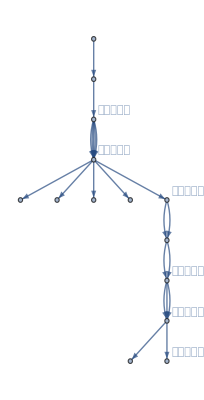

```mathematica
g=Graph[storyVocLGrSel[4,"voc"]["20231001"][[id]],VertexLabels->vl,EdgeLabels->None]
```

キーワードの時間的変遷：
同じキーワードが続く場合はページを進めているとみて良い。
Nullは詳細ページへの移動とみて良い。

```mathematica
kws[id]=GtoKWSeq[storyVocLGrSel[4,"voc"]["20231001"][[id]]]
```

{{Null,{3.90518×10^9}},{中国自動車,{3.90518×10^9}},{中国自動車,{3.90518×10^9,3.90518×10^9,3.90518×10^9,3.90518×10^9,3.90518×10^9}},{Null,{3.90518×10^9}},{Null,{3.90518×10^9}},{Null,{3.90518×10^9}},{Null,{3.90518×10^9}},{中国自動車,{3.90518×10^9}},{Null,{3.90518×10^9,3.90518×10^9}},{中国自動車,{3.90518×10^9,3.90518×10^9}},{自動車輸出,{3.90518×10^9,3.90518×10^9,3.90518×10^9}},{Null,{3.90518×10^9}},{自動車輸出,{3.90518×10^9}}}

```mathematica
KWSeqSplitGather[kws[id]]//TableForm
```

中国自動車
自動車輸出

### キーワード入力回数とキーワード個数

```mathematica
storyVocLGrSel[4,"voc"]["20231001"]//Length
```

121359

```mathematica
(celGraph["20231001"][40]=Cases[storyVocLGrSel[4,"voc"]["20231001"],x_/;VertexCount[x]<=40])//Length
```

121025

キーワードなしは除く。

```mathematica
(kwsSplit["20231001"][40]=Cases[Map[KWSeqSplitGather[GtoKWSeq[#]]&,celGraph["20231001"][40]],x_/;Length[x]>0])//Length
```

19180

各プロパティ：

```mathematica
(kwsprop["20231001"][40]["input count"]=Map[Length,kwsSplit["20231001"][40]])//Length
```

19180

```mathematica
(kwsprop["20231001"][40]["input appearance count"]=Map[Tally,kwsSplit["20231001"][40]])//Length
```

19180

```mathematica
(kwsprop["20231001"][40]["input split"]=Map[StringSplit[#," "]&,kwsSplit["20231001"][40]])//Length
```

19180

```mathematica
(kwsprop["20231001"][40]["input split count"]=Map[Length,kwsprop["20231001"][40]["input split"],{2}])//Length
```

19180